#### Born Oppenheimer Approximation

a) Making the BO approximation, write the purely electronic Hamiltonian and, by completing the square,
write its energy levels, E_(el,n)(X).

```mathematica
ϕ[x_]:=(Subscript[ω, el]/π)^(1/4)Exp[-Subscript[ω, el]*x^2/2]
Integrate[-ϕ[x] 1/2 D[ϕ[x],{x,2}],{x,-∞,∞},Assumptions->Re[Subscript[ω, el]]>0]
```

ω_el/4

```mathematica
Integrate[1/2 Subscript[ω, el]^2 x^2 ϕ[x]^2,{x,-∞,∞},Assumptions->Re[Subscript[ω, el]]>0]
```

ω_el/4

```mathematica
Integrate[-ϕ[x] 1/2 D[ϕ[x],{x,2}],{x,-∞,∞},Assumptions->Re[Subscript[ω, el]]>0]
```

ω_el/4

```mathematica
Integrate[1/2 Subscript[ω, el]^2(x-X)^2 ϕ[x]^2,{x,-∞,∞},Assumptions->Re[Subscript[ω, el]]>0]
```

1/4 ω_el (1+2 X^2 ω_el)

```mathematica
Integrate[x*X*ϕ[x]^2,{x,-∞,∞},Assumptions->Re[Subscript[ω, el]]>0]
```

0

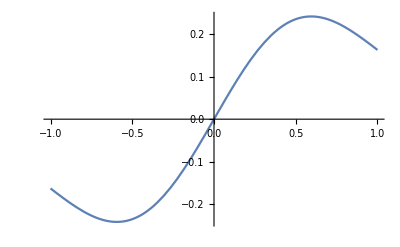

```mathematica
Plot[x*ϕ[x]^2/.Subscript[ω, el]->Sqrt[2],{x,-1,1}]
```

```mathematica
ϕ2[x_]:=(Subscript[ω, el]/π)^(1/4)(2 Subscript[ω, el])^(1/2)x Exp[-Subscript[ω, el]*x^2/2]
Integrate[-ϕ2[x] 1/2 D[ϕ2[x],{x,2}],{x,-∞,∞},Assumptions->Re[Subscript[ω, el]]>0]
Integrate[1/2 Subscript[ω, el]^2(x-X)^2 ϕ2[x]^2,{x,-∞,∞},Assumptions->Re[Subscript[ω, el]]>0]
Integrate[x*X*ϕ2[x]^2,{x,-∞,∞},Assumptions->Re[Subscript[ω, el]]>0]
```

(3 ω_el)/4

1/4 ω_el (3+2 X^2 ω_el)

0

```mathematica
Eelec[n_]:=(n+1/2)Subscript[ω, el]+(X^2 Subscript[ω, el]^2)/2
```

b) Write the nuclear equation for the proton in the field of the electronic energy plus any other
parts of the potential, to get an expression for the total energy of the system, E_(ν,n), where ν is the
quantum number for proton vibrations.

```mathematica
ϕnuc[x_]:=((m*Subscript[ω, nuc])/π)^(1/4)Exp[-m*Subscript[ω, nuc]*x^2/2]
```

```mathematica
Integrate[-ϕnuc[X] 1/(2*m)D[ϕnuc[X],{X,2}],{X,-∞,∞},Assumptions->{Re[Subscript[ω, nuc]]>0,Re[m]>0,Re[m Subscript[ω, nuc]]≥0}]
```

ω_nuc/4

```mathematica
Integrate[(X^2 m Subscript[ω, nuc]^2)/2*ϕnuc[X]^2,{X,-∞,∞},Assumptions->{Re[Subscript[ω, nuc]]>0,Re[m]>0,Re[m Subscript[ω, nuc]]>0}]
```

ω_nuc/4

```mathematica
ϕnuc1[x_]:=((m*Subscript[ω, nuc])/π)^(1/4)Sqrt[2m Subscript[ω, nuc]]x Exp[-m*Subscript[ω, nuc]*x^2/2]
Integrate[-ϕnuc1[X] 1/(2*m)D[ϕnuc1[X],{X,2}],{X,-∞,∞},Assumptions->{Re[Subscript[ω, nuc]]>0,Re[m]>0,Re[m Subscript[ω, nuc]]≥0}]
```

(3 ω_nuc)/4

```mathematica
Integrate[(X^2 m Subscript[ω, nuc]^2)/2*ϕnuc1[X]^2,{X,-∞,∞},Assumptions->{Re[Subscript[ω, nuc]]>0,Re[m]>0,Re[m Subscript[ω, nuc]]>0}]
```

(3 ω_nuc)/4

```mathematica
Etot[ν_,n_,m_]:=(ν+1/2 )Subscript[ω, nuc]/2+(n+1/2)Subscript[ω, el]+(3 Subscript[ω, el]^2)/(4m Subscript[ω, nuc])
```

c) Assuming m=25, plot the lowest 12 levels, labeling them with their electronic and nuclear quantum
numbers.

```mathematica
Etot[ν_,n_,m_]:=(ν+2 )Sqrt[2]/(2 Sqrt[m])+(n+1/2)Sqrt[2]
```

```mathematica
Etot[0,0,25]//N
```

0.989949

```mathematica
nstate[ν_,n_,m_]:=Table[{n,Etot[i,n,m]}//N,{i,0,ν}]
```

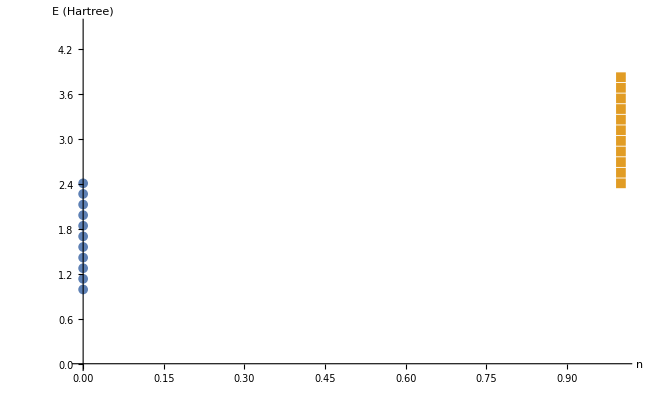

```mathematica
ListPlot[Table[nstate[10,i,25],{i,0,1}],AxesLabel->{"n","E (Hartree)"},
PlotMarkers->{Automatic,Medium},TicksStyle->Large,AxesStyle->Large,
PlotRange->{0,4.5}]
```

```mathematica
nstate[12,0,25]
```

{{0.,0.989949},{0.,1.13137},{0.,1.27279},{0.,1.41421},{0.,1.55563},{0.,1.69706},{0.,1.83848},{0.,1.9799},{0.,2.12132},{0.,2.26274},{0.,2.40416},{0.,2.54558},{0.,2.68701}}

```mathematica
nstate[12,1,25]
```

```mathematica
{{1.,2.4041630560342613},{1.,2.5455844122715714},{1.,2.6870057685088806},{1.,2.8284271247461903},{1.,2.9698484809834995},{1.,3.1112698372208096},{1.,6911934581184},{1.,3.394112549695428},{1.,3.5355339059327378},{1.,3.6769552621700474},{1.,3.818376618407356},{1.,3.9597979746446663},{1.,4.1012193308819755}}
```

```mathematica
nstate[12,2,25]
```

{{2.,3.81838},{2.,3.9598},{2.,4.10122},{2.,4.24264},{2.,4.38406},{2.,4.52548},{2.,4.6669},{2.,4.80833},{2.,4.94975},{2.,5.09117},{2.,5.23259},{2.,5.37401},{2.,5.51543}}

d) The exact solution to this problem is given by the sum of two harmonic oscillators. Show that, if m>>1,
this agrees with your BO solutions above.

```mathematica
exactp[m_]:=1+1/m+Sqrt[1-1/m+1/m^2]
exactm[m_]:=1+1/m-Sqrt[1-1/m+1/m^2]
```

```mathematica
exactp[25]//N
```

2.02061

```mathematica
exactm[25]//N
```

0.0593879